## Método de Bisección

Teorema (Bisección ).  Sea  f∈C[a,b] existe un número  r∈[a,b] tal que  f(r)=0.  
Si  f(a) y  f(b) tienen signos opuestos, y {c_n} representa los puntos medios generados por el proceso de bisección, entonces

		|r-c_n| ≤(b - a)/2^(n+1)   para   n=0,1,...,

y la sucesión {c_n} converge al cero en  x=r.  

Es decir,  	lim_(k → ∞) c_n = r.

### Módulo

```mathematica
Biseccion[a0_,b0_,m_] :=
Module[{},
a = N[a0];  
b = N[b0];  
c = (a + b)/2; 
k = 0; 
output={{k,a,c,b,f[c]}}; 
While[k < m,
If[ Sign[f[b]] ==  Sign[f[c]], 
b = c, a = c; ]; 
c = (a + b)/2; 
k = k+1; 
output=Append[output,{k,a,c,b,f[c]}]; ]; 
Print[NumberForm[TableForm[output,
TableHeadings->{None,{"k","a_k","c_k","b_k","f[c_k]"}}],16]]; 
Print["  c  = ",NumberForm[c,16] ]; 
Print[" Δc  = ±",(b-a)/2]; 
Print["f[c] = ",NumberForm[f[c],16] ]; ]
```

Ejercicio.  Encuentre todas las soluciones reales de la siguiente ecuación  x^3+4 x^2-10=0.  
Ayuda: Grafique la ecuacion primero y observe algún intervalo donde se encuentre la solución

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x^3+4 x^2-10
```

```mathematica
N[1/3 (-4+(71-3 √105)^(1/3)+(71+3 √105)^(1/3))]
```

1.36523

```mathematica
Solve[f[x]=0,x]
```

Solve::naqs: 0 is not a quantified system of equations and inequalities.

Solve[0,x]

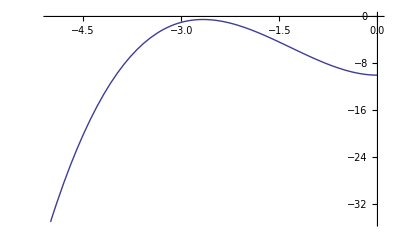

```mathematica
Plot[f[x],{x,-5,0}]
```

```mathematica
Biseccion[1.36,1.37,15]
```

k | a_k | c_k | b_k | f[c_k]
0 | 1.36 | 1.365 | 1.37 | -0.003797874999996509
1 | 1.365 | 1.3675 | 1.37 | 0.03752692187500273
2 | 1.365 | 1.36625 | 1.3675 | 0.01685186914062697
3 | 1.365 | 1.365625 | 1.36625 | 0.006523834228516989
4 | 1.365 | 1.3653125 | 1.365625 | 0.001362188995363667
5 | 1.365 | 1.36515625 | 1.3653125 | -0.001218040645598606
6 | 1.36515625 | 1.365234375 | 1.3653125 | 0.00007202476263046265
7 | 1.36515625 | 1.3651953125 | 1.365234375 | -0.0005730202943681206
8 | 1.3651953125 | 1.36521484375 | 1.365234375 | -0.0002505008541113796
9 | 1.36521484375 | 1.365224609375 | 1.365234375 | -0.0000892388178037606
10 | 1.365224609375 | 1.3652294921875 | 1.365234375 | -8.60722060380681×10^-6
11 | 1.3652294921875 | 1.36523193359375 | 1.365234375 | 0.00003170872275859438
12 | 1.3652294921875 | 1.365230712890625 | 1.36523193359375 | 0.00001155073901237813
13 | 1.3652294921875 | 1.365230102539063 | 1.365230712890625 | 1.471756188919926×10^-6
14 | 1.3652294921875 | 1.365229797363281 | 1.365230102539063 | -3.567732960618741×10^-6
15 | 1.365229797363281 | 1.365229949951172 | 1.365230102539063 | -1.04798857591959×10^-6

c  = 1.365229949951172

Δc  = ±1.52588×10^-7

f[c] = -1.04798857591959×10^-6

Ejercicio (convergencia lenta).  Encuentre  la solución real de la siguiente ecuación  1-10 x+25 x^2 = 0.  p_0=1.0  y  p_1=0.9.

```mathematica
Clear[f]
```

```mathematica
f[x_]:=1-10 x+25 x^2
```

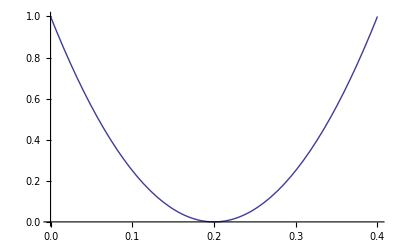

```mathematica
Plot[f[x],{x,0,0.4}]
```

```mathematica
Biseccion[0.15,0.35,15]
```

k | a_k | c_k | b_k | f[c_k]
0 | 0.15 | 0.25 | 0.35 | 0.0625
1 | 0.15 | 0.2 | 0.25 | 2.220446049250313×10^-16
2 | 0.15 | 0.175 | 0.2 | 0.01562499999999989
3 | 0.15 | 0.1625 | 0.175 | 0.03515625
4 | 0.15 | 0.15625 | 0.1625 | 0.0478515625
5 | 0.15 | 0.153125 | 0.15625 | 0.05493164062500011
6 | 0.15 | 0.1515625 | 0.153125 | 0.05865478515624989
7 | 0.15 | 0.15078125 | 0.1515625 | 0.06056213378906261
8 | 0.15 | 0.150390625 | 0.15078125 | 0.06152725219726562
9 | 0.15 | 0.1501953125 | 0.150390625 | 0.06201267242431641
10 | 0.15 | 0.15009765625 | 0.1501953125 | 0.062256097793579
11 | 0.15 | 0.150048828125 | 0.15009765625 | 0.06237798929214488
12 | 0.15 | 0.1500244140625 | 0.150048828125 | 0.06243897974491119
13 | 0.15 | 0.15001220703125 | 0.1500244140625 | 0.0624694861471654
14 | 0.15 | 0.150006103515625 | 0.15001220703125 | 0.06248474214225997
15 | 0.15 | 0.1500030517578125 | 0.150006103515625 | 0.06249237083829939

c  = 0.1500030517578125

Δc  = ±3.05176×10^-6

f[c] = 0.06249237083829939

Ejercicio (convergencia oscilatoria).  Encuentre  la solución real de la siguiente ecuación  ArcTan[x]= 0. p_0=1.35  y  p_1=1.30.  (p_0=1.60;  y  p_1=1.50.  )

```mathematica
f[x_]:=ArcTan[x]
```

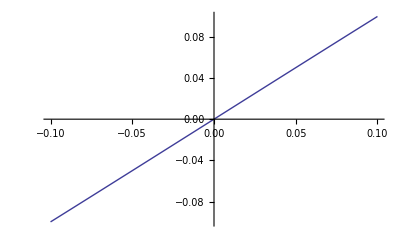

```mathematica
Plot[f[x],{x,-0.1,0.1}]
```

```mathematica
Biseccion[-0.1,0.1,15]
```

k | a_k | c_k | b_k | f[c_k]
0 | -0.1 | 0. | 0.1 | 0.
1 | 0. | 0.05 | 0.1 | 0.04995839572194277
2 | 0. | 0.025 | 0.05 | 0.02499479361892016
3 | 0. | 0.0125 | 0.025 | 0.01249934901936168
4 | 0. | 0.00625 | 0.0125 | 0.006249918621698962
5 | 0. | 0.003125 | 0.00625 | 0.003124989827533563
6 | 0. | 0.0015625 | 0.003125 | 0.001562498728436108
7 | 0. | 0.00078125 | 0.0015625 | 0.0007812498410543389
8 | 0. | 0.000390625 | 0.00078125 | 0.0003906249801317869
9 | 0. | 0.0001953125 | 0.000390625 | 0.0001953124975164732
10 | 0. | 0.00009765625 | 0.0001953125 | 0.0000976562496895592
11 | 0. | 0.000048828125 | 0.00009765625 | 0.0000488281249611949
12 | 0. | 0.0000244140625 | 0.000048828125 | 0.00002441406249514936
13 | 0. | 0.00001220703125 | 0.0000244140625 | 0.00001220703124939367
14 | 0. | 6.103515625×10^-6 | 0.00001220703125 | 6.10351562492421×10^-6
15 | 0. | 3.0517578125×10^-6 | 6.103515625×10^-6 | 3.051757812490526×10^-6

c  = 3.0517578125×10^-6

Δc  = ±3.05176×10^-6

f[c] = 3.051757812490526×10^-6

Ejercicio (divergencia).  Encuentre  la solución real de la siguiente ecuación   x ⅇ^-x = 0. p_0=1.5  y  p_1=2.0.

```mathematica
f[x_]:=x ⅇ^-x
```

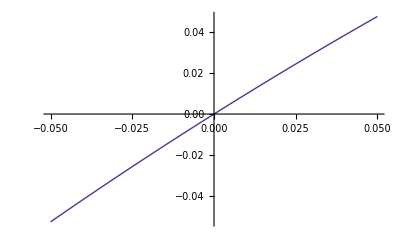

```mathematica
Plot[f[x],{x,-0.05,0.05}]
```

```mathematica
Biseccion[-0.05,0.05,15]
```

k | a_k | c_k | b_k | f[c_k]
0 | -0.05 | 0. | 0.05 | 0.
1 | 0. | 0.025 | 0.05 | 0.02438274780070832
2 | 0. | 0.0125 | 0.025 | 0.01234472250617352
3 | 0. | 0.00625 | 0.0125 | 0.006211059316396216
4 | 0. | 0.003125 | 0.00625 | 0.003115249617906901
5 | 0. | 0.0015625 | 0.003125 | 0.00156006050010561
6 | 0. | 0.00078125 | 0.0015625 | 0.0007806398867940032
7 | 0. | 0.000390625 | 0.00078125 | 0.0003904724419078173
8 | 0. | 0.0001953125 | 0.000390625 | 0.0001952743567523916
9 | 0. | 0.00009765625 | 0.0001953125 | 0.0000976467137224821
10 | 0. | 0.000048828125 | 0.00009765625 | 0.0000488257408724157
11 | 0. | 0.0000244140625 | 0.000048828125 | 0.00002441346646082815
12 | 0. | 0.00001220703125 | 0.0000244140625 | 0.00001220688223929755
13 | 0. | 6.103515625×10^-6 | 0.00001220703125 | 6.103478372210702×10^-6
14 | 0. | 3.0517578125×10^-6 | 6.103515625×10^-6 | 3.051748499288465×10^-6
15 | 0. | 1.52587890625×10^-6 | 3.0517578125×10^-6 | 1.52587657794534×10^-6

c  = 1.52587890625×10^-6

Δc  = ±1.52588×10^-6

f[c] = 1.52587657794534×10^-6

## Método de la secante

Teorema (Secant Method).  Sea f∈C^2[a,b] existe un número  p∈[a,b], tal que f(p)=0.  Si   f'(p)≠0, entonces existe un  δ>0 de tal manera que la sucesión{p_k}_(k=0)^∞  definida por la iteracción 

	p_(k+1) = g(p_(k-1),p_k) = p_k - (f(p_k)(p_k -  p_(k-1)))/(f(p_k) -  f(p_(k-1)))    para   k=0,1,...  

converge  a p para cierta aproximación inicial  p_0,p_1∈[p-δ,p+δ].

### Módulo

```mathematica
Secante[x0_,x1_,max_]:=
Module[{},
k = 1; 
p0 = N[x0]; 
p1 = N[x1]; 
Print["f[x] = ",f[x] ];
Print["p_(k + 1) = g[p_k,p_(k - 1)] = p_k - (f[SubscriptBox[p, k]] (SubscriptBox[p, k] - SubscriptBox[p, k - 1]))/(f[SubscriptBox[p, k]] - f[SubscriptBox[p, k - 1]])"]; 
Print["p_0 = ",PaddedForm[p0,{16,16}],",   f[p_0] = ",NumberForm[f[p0],16] ]; 
Print["p_1 = ",PaddedForm[p1,{16,16}],",   f[p_1] = ",NumberForm[f[p1],16] ];  
p2 = p1; 
p1 = p0; 
While[ k<max,
p0 = p1; 
p1 = p2; 
p2 = p1 - (f[p1](p1 - p0))/(f[p1] - f[p0]); 
k = k+1; 
Print[Subscript["p", k]," = ",PaddedForm[p2,{16,16}],",   f[",Subscript["p", k],"] = ",NumberForm[f[p2],16] ]; ]; 
Print[""]; 
Print["f[x] = ",f[x] ];
Print["  p  = ",NumberForm[p2,16] ]; 
Print[" Δp  = ±",Abs[p2-p1] ]; 
Print["f[p] = ",NumberForm[f[p2],16] ]; ]
```

```mathematica
■_□
```

Ejercicio (convergencia rápida).  Encuentre  la solución real de la siguiente ecuación  3Exp[x]-4Cos[x] = 0. p_0=1.0  y  p_1=0.9.

```mathematica
Clear[f]
```

```mathematica
f[x_]:= 3Exp[x]-4Cos[x]
```

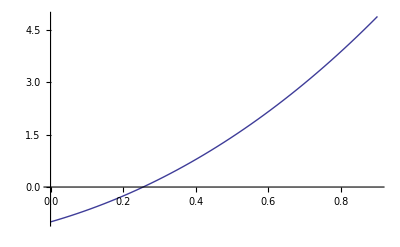

```mathematica
Plot[f[x],{x,0,0.9}]
```

```mathematica
Secante[0,0.9,9]
```

f[x] = 3 ⅇ^x-4 Cos[x]

p_(k + 1) = g[p_k,p_(k - 1)] = p_k - (f[SubscriptBox[p, k]] (SubscriptBox[p, k] - SubscriptBox[p, k - 1]))/(f[SubscriptBox[p, k]] - f[SubscriptBox[p, k - 1]])

p_0 =  0.0000000000000000,   f[p_0] = -1.

p_1 =  0.9000000000000000,   f[p_1] = 4.892369460388192

p_2 =  0.1527399132132334,   f[p_2] = -0.4583658799198562

p_3 =  0.2167532694016345,   f[p_3] = -0.1802905022272534

p_4 =  0.2582564051061442,   f[p_4] = 0.0166651956795274

p_5 =  0.2547446616776448,   f[p_5] = -0.0005142123560584189

p_6 =  0.2548497748374523,   f[p_6] = -1.386627970667575×10^-6

p_7 =  0.2548500590526145,   f[p_7] = 1.159512486026415×10^-10

p_8 =  0.2548500590288501,   f[p_8] = -8.88178419700125×10^-16

p_9 =  0.2548500590288503,   f[p_9] = 0.

f[x] = 3 ⅇ^x-4 Cos[x]

p  = 0.2548500590288503

Δp  = ±1.66533×10^-16

f[p] = 0.

Ejercicio (convergencia lenta).  Encuentre  la solución real de la siguiente ecuación  1-10 x+25 x^2 = 0.  p_0=1.0  y  p_1=0.9.

-Graphics-

```mathematica
Secante[0.15,0.35,15]
```

f[x] = 1-10 x+25 x^2

p_(k + 1) = g[p_k,p_(k - 1)] = p_k - (f[SubscriptBox[p, k]] (SubscriptBox[p, k] - SubscriptBox[p, k - 1]))/(f[SubscriptBox[p, k]] - f[SubscriptBox[p, k - 1]])

p_0 =  0.1500000000000000,   f[p_0] = 0.0625

p_1 =  0.3500000000000000,   f[p_1] = 0.5624999999999996

p_2 =  0.1250000000000000,   f[p_2] = 0.140625

p_3 =  0.0499999999999999,   f[p_3] = 0.5625000000000012

p_4 =  0.1500000000000000,   f[p_4] = 0.06250000000000011

p_5 =  0.1625000000000000,   f[p_5] = 0.03515625

p_6 =  0.1785714285714285,   f[p_6] = 0.01147959183673486

p_7 =  0.1863636363636364,   f[p_7] = 0.004648760330578483

p_8 =  0.1916666666666666,   f[p_8] = 0.00173611111111116

p_9 =  0.1948275862068967,   f[p_9] = 0.0006688466111770541

p_10 =  0.1968085106382974,   f[p_10] = 0.0002546401086465089

p_11 =  0.1980263157894737,   f[p_11] = 0.0000973857340719198

p_12 =  0.1987804878048768,   f[p_12] = 0.00003718024985133184

p_13 =  0.1992462311557787,   f[p_13] = 0.00001420418676301161

p_14 =  0.1995341614906847,   f[p_14] = 5.42513791901289×10^-6

p_15 =  0.1997120921305171,   f[p_15] = 2.072273532660596×10^-6

f[x] = 1-10 x+25 x^2

p  = 0.1997120921305171

Δp  = ±0.000177931

f[p] = 2.072273532660596×10^-6

Ejercicio (convergencia oscilatoria).  Encuentre  la solución real de la siguiente ecuación  ArcTan[x]= 0. p_0=1.35  y  p_1=1.30.  (p_0=1.60;  y  p_1=1.50.  )

-Graphics-

```mathematica
Secante[-0.1,0.1,3]
```

f[x] = ArcTan[x]

p_(k + 1) = g[p_k,p_(k - 1)] = p_k - (f[SubscriptBox[p, k]] (SubscriptBox[p, k] - SubscriptBox[p, k - 1]))/(f[SubscriptBox[p, k]] - f[SubscriptBox[p, k - 1]])

p_0 = -0.1000000000000000,   f[p_0] = -0.099668652491162

p_1 =  0.1000000000000000,   f[p_1] = 0.099668652491162

p_2 =  0.0000000000000000,   f[p_2] = 0.

p_3 =  0.0000000000000000,   f[p_3] = 0.

f[x] = ArcTan[x]

p  = 0.

Δp  = ±0.

f[p] = 0.

Ejercicio (divergencia).  Encuentre  la solución real de la siguiente ecuación   x ⅇ^-x = 0. p_0=1.5  y  p_1=2.0.

-Graphics-

```mathematica
Secante[-0.05,0.05,9]
```

f[x] = ⅇ^-x x

p_(k + 1) = g[p_k,p_(k - 1)] = p_k - (f[SubscriptBox[p, k]] (SubscriptBox[p, k] - SubscriptBox[p, k - 1]))/(f[SubscriptBox[p, k]] - f[SubscriptBox[p, k - 1]])

p_0 = -0.0500000000000000,   f[p_0] = -0.05256355481880121

p_1 =  0.0500000000000000,   f[p_1] = 0.0475614712250357

p_2 =  0.0024979187478940,   f[p_2] = 0.002491686936342705

p_3 = -0.0001282379371882,   f[p_3] = -0.00012825438321118

p_4 =  3.2070775067615050×10^-7,   f[p_4] = 3.207076478227056×10^-7

p_5 =  4.1124270078989710×10^-11,   f[p_5] = 4.11242700772985×10^-11

p_6 = -1.3188874279747040×10^-17,   f[p_6] = -1.318887427974704×10^-17

p_7 =  5.4238193168228890×10^-28,   f[p_7] = 5.423819316822889×10^-28

p_8 = -8.9683101716788300×10^-44,   f[p_8] = -8.96831017167883×10^-44

p_9 =  0.0000000000000000,   f[p_9] = 0.

f[x] = ⅇ^-x x

p  = 0.

Δp  = ±8.96831×10^-44

f[p] = 0.

## Método de Newton Raphson

Teorema (Newton-Raphson ).  Sea f∈C^2[a,b] existe un número p∈[a,b], donde f(p)=0.  Si  f'(p)≠0, entonces existe un δ>0 tal que la sucesión {p_k}_(k=0)^∞ definida por la iteracción  

	p_(k+1) = g(p_k) =  p_k -(f(p_k))/(f'(p_k))    for    k=0,1,...  

converge a  p para alguna condición inicial  p_0∈[p-δ,p+δ].

### Módulo

```mathematica
NewtonRaphson[x0_,max_]:=
Module[{},
k = 0; 
p0 = N[x0]; 
Print["f[x] = ",f[x] ];
g[x_]=x-f[x]/f'[x]; 
Print["g[x] = x - f[x]/f'[x]"]; 
Print["g[x] = ",g[x] ];
Print["g[x] = ",Simplify[g[x]]];
Print["  p_0 = ",PaddedForm[p0,{16,16}],",   f[p_0] = ",NumberForm[f[p0],16] ]; 
p1 = p0; 
While[ k<max,
p0 = p1; 
p1 = p0 - f[p0]/f'[p0]; 
k = k+1;  
Print[Subscript["  p", k]," = ",PaddedForm[p1,{16,16}],",   f[",Subscript["p", k],"] = ",NumberForm[f[p1],16] ]; ]; 
Print[""]; 
Print["f[x] = ",f[x] ];
Print["  p  = ",NumberForm[p1,16] ]; 
Print[" Δp  = ±",Abs[p1-p0] ]; 
Print["f[p] = ",NumberForm[f[p1],16] ]; ]
```

```mathematica
NewtonRaphson[0.2,15]
```

f[x] = 3 ⅇ^x-4 Cos[x]

g[x] = x - f[x]/f'[x]

g[x] = x-(3 ⅇ^x-4 Cos[x])/(3 ⅇ^x+4 Sin[x])

g[x] = x+(-3 ⅇ^x+4 Cos[x])/(3 ⅇ^x+4 Sin[x])

p_0 =  0.2000000000000000,   f[p_0] = -0.2560580368844567

p_1 =  0.2574264648141660,   f[p_1] = 0.01259651578613141

p_2 =  0.2548553069076384,   f[p_2] = 0.00002560558659725487

p_3 =  0.2548500590506984,   f[p_3] = 1.066018384676681×10^-10

p_4 =  0.2548500590288503,   f[p_4] = 0.

p_5 =  0.2548500590288503,   f[p_5] = 0.

p_6 =  0.2548500590288503,   f[p_6] = 0.

p_7 =  0.2548500590288503,   f[p_7] = 0.

p_8 =  0.2548500590288503,   f[p_8] = 0.

p_9 =  0.2548500590288503,   f[p_9] = 0.

p_10 =  0.2548500590288503,   f[p_10] = 0.

p_11 =  0.2548500590288503,   f[p_11] = 0.

p_12 =  0.2548500590288503,   f[p_12] = 0.

p_13 =  0.2548500590288503,   f[p_13] = 0.

p_14 =  0.2548500590288503,   f[p_14] = 0.

p_15 =  0.2548500590288503,   f[p_15] = 0.

f[x] = 3 ⅇ^x-4 Cos[x]

p  = 0.2548500590288503

Δp  = ±0.

f[p] = 0.

-Graphics-

Ejercicio (convergencia lenta).  Encuentre  la solución real de la siguiente ecuación  1-10 x+25 x^2 = 0.  p_0=1.0  y  p_1=0.9.

-Graphics-

```mathematica
NewtonRaphson[0.25,15]
```

f[x] = 1-10 x+25 x^2

g[x] = x - f[x]/f'[x]

g[x] = x-(1-10 x+25 x^2)/(-10+50 x)

g[x] = 1/10 (1+5 x)

p_0 =  0.2500000000000000,   f[p_0] = 0.0625

p_1 =  0.2250000000000000,   f[p_1] = 0.015625

p_2 =  0.2125000000000000,   f[p_2] = 0.003906249999999778

p_3 =  0.2062500000000004,   f[p_3] = 0.0009765625

p_4 =  0.2031250000000005,   f[p_4] = 0.000244140625

p_5 =  0.2015625000000008,   f[p_5] = 0.00006103515625

p_6 =  0.2007812500000012,   f[p_6] = 0.0000152587890625

p_7 =  0.2003906250000017,   f[p_7] = 3.814697265625×10^-6

p_8 =  0.2001953125000026,   f[p_8] = 9.5367431640625×10^-7

p_9 =  0.2000976562500039,   f[p_9] = 2.384185793236071×10^-7

p_10 =  0.2000488281249604,   f[p_10] = 5.960464477539062×10^-8

p_11 =  0.2000244140624406,   f[p_11] = 1.490116119384766×10^-8

p_12 =  0.2000122070311609,   f[p_12] = 3.725290298461914×10^-9

p_13 =  0.2000061035154914,   f[p_13] = 9.31322352570874×10^-10

p_14 =  0.2000030517583396,   f[p_14] = 2.328306436538696×10^-10

p_15 =  0.2000015258796970,   f[p_15] = 5.820766091346741×10^-11

f[x] = 1-10 x+25 x^2

p  = 0.200001525879697

Δp  = ±1.52588×10^-6

f[p] = 5.820766091346741×10^-11

Ejercicio (convergencia oscilatoria).  Encuentre  la solución real de la siguiente ecuación  ArcTan[x]= 0. p_0=1.35  y  p_1=1.30.  (p_0=1.60;  y  p_1=1.50.  )

-Graphics-

```mathematica
NewtonRaphson[0,0]
```

f[x] = ⅇ^-x x

g[x] = x - f[x]/f'[x]

g[x] = x-(ⅇ^-x x)/(ⅇ^-x-ⅇ^-x x)

g[x] = x^2/(-1+x)

p_0 =  0.0000000000000000,   f[p_0] = 0.

f[x] = ⅇ^-x x

p  = 0.

Δp  = ±0.

f[p] = 0.

Ejercicio (divergencia).  Encuentre  la solución real de la siguiente ecuación   x ⅇ^-x = 0. p_0=1.5  y  p_1=2.0.

-Graphics-

```mathematica
NewtonRaphson[0,0]
```

f[x] = ⅇ^-x x

g[x] = x - f[x]/f'[x]

g[x] = x-(ⅇ^-x x)/(ⅇ^-x-ⅇ^-x x)

g[x] = x^2/(-1+x)

p_0 =  0.0000000000000000,   f[p_0] = 0.

f[x] = ⅇ^-x x

p  = 0.

Δp  = ±0.

f[p] = 0.